```mathematica
"definição do estadio"
a=1
b=1
```

definição do estadio

1

1

```mathematica
"definição do retângulo"
A=a+b
B=b
```

definição do retângulo

2

1

```mathematica
"definição da barreira de potencial Ka"
Ka=1000
```

definição da barreira de potencial Ka

1000

```mathematica
"definição da base harmonica e de seus autovalores"
φ[x_,y_,n_,m_]=2/(√(A*B))Sin[π*n(x/A)]Sin[π*m(y/B)]
nM=10
mM=10
Base[x_,y_]=Table[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM],{i,0,nM*mM-1}]
κ[n_,m_]=π √((n/A)^2+(m/B)^2)
```

definição da base harmonica e de seus autovalores

√2 Sin[(n π x)/2] Sin[m π y]

10

10

{√2 Sin[(π x)/2] Sin[π y],√2 Sin[π x] Sin[π y],√2 Sin[(3 π x)/2] Sin[π y],√2 Sin[2 π x] Sin[π y],√2 Sin[(5 π x)/2] Sin[π y],√2 Sin[3 π x] Sin[π y],√2 Sin[(7 π x)/2] Sin[π y],√2 Sin[4 π x] Sin[π y],√2 Sin[(9 π x)/2] Sin[π y],√2 Sin[5 π x] Sin[π y],√2 Sin[(π x)/2] Sin[2 π y],√2 Sin[π x] Sin[2 π y],√2 Sin[(3 π x)/2] Sin[2 π y],√2 Sin[2 π x] Sin[2 π y],√2 Sin[(5 π x)/2] Sin[2 π y],√2 Sin[3 π x] Sin[2 π y],√2 Sin[(7 π x)/2] Sin[2 π y],√2 Sin[4 π x] Sin[2 π y],√2 Sin[(9 π x)/2] Sin[2 π y],√2 Sin[5 π x] Sin[2 π y],√2 Sin[(π x)/2] Sin[3 π y],√2 Sin[π x] Sin[3 π y],√2 Sin[(3 π x)/2] Sin[3 π y],√2 Sin[2 π x] Sin[3 π y],√2 Sin[(5 π x)/2] Sin[3 π y],√2 Sin[3 π x] Sin[3 π y],√2 Sin[(7 π x)/2] Sin[3 π y],√2 Sin[4 π x] Sin[3 π y],√2 Sin[(9 π x)/2] Sin[3 π y],√2 Sin[5 π x] Sin[3 π y],√2 Sin[(π x)/2] Sin[4 π y],√2 Sin[π x] Sin[4 π y],√2 Sin[(3 π x)/2] Sin[4 π y],√2 Sin[2 π x] Sin[4 π y],√2 Sin[(5 π x)/2] Sin[4 π y],√2 Sin[3 π x] Sin[4 π y],√2 Sin[(7 π x)/2] Sin[4 π y],√2 Sin[4 π x] Sin[4 π y],√2 Sin[(9 π x)/2] Sin[4 π y],√2 Sin[5 π x] Sin[4 π y],√2 Sin[(π x)/2] Sin[5 π y],√2 Sin[π x] Sin[5 π y],√2 Sin[(3 π x)/2] Sin[5 π y],√2 Sin[2 π x] Sin[5 π y],√2 Sin[(5 π x)/2] Sin[5 π y],√2 Sin[3 π x] Sin[5 π y],√2 Sin[(7 π x)/2] Sin[5 π y],√2 Sin[4 π x] Sin[5 π y],√2 Sin[(9 π x)/2] Sin[5 π y],√2 Sin[5 π x] Sin[5 π y],√2 Sin[(π x)/2] Sin[6 π y],√2 Sin[π x] Sin[6 π y],√2 Sin[(3 π x)/2] Sin[6 π y],√2 Sin[2 π x] Sin[6 π y],√2 Sin[(5 π x)/2] Sin[6 π y],√2 Sin[3 π x] Sin[6 π y],√2 Sin[(7 π x)/2] Sin[6 π y],√2 Sin[4 π x] Sin[6 π y],√2 Sin[(9 π x)/2] Sin[6 π y],√2 Sin[5 π x] Sin[6 π y],√2 Sin[(π x)/2] Sin[7 π y],√2 Sin[π x] Sin[7 π y],√2 Sin[(3 π x)/2] Sin[7 π y],√2 Sin[2 π x] Sin[7 π y],√2 Sin[(5 π x)/2] Sin[7 π y],√2 Sin[3 π x] Sin[7 π y],√2 Sin[(7 π x)/2] Sin[7 π y],√2 Sin[4 π x] Sin[7 π y],√2 Sin[(9 π x)/2] Sin[7 π y],√2 Sin[5 π x] Sin[7 π y],√2 Sin[(π x)/2] Sin[8 π y],√2 Sin[π x] Sin[8 π y],√2 Sin[(3 π x)/2] Sin[8 π y],√2 Sin[2 π x] Sin[8 π y],√2 Sin[(5 π x)/2] Sin[8 π y],√2 Sin[3 π x] Sin[8 π y],√2 Sin[(7 π x)/2] Sin[8 π y],√2 Sin[4 π x] Sin[8 π y],√2 Sin[(9 π x)/2] Sin[8 π y],√2 Sin[5 π x] Sin[8 π y],√2 Sin[(π x)/2] Sin[9 π y],√2 Sin[π x] Sin[9 π y],√2 Sin[(3 π x)/2] Sin[9 π y],√2 Sin[2 π x] Sin[9 π y],√2 Sin[(5 π x)/2] Sin[9 π y],√2 Sin[3 π x] Sin[9 π y],√2 Sin[(7 π x)/2] Sin[9 π y],√2 Sin[4 π x] Sin[9 π y],√2 Sin[(9 π x)/2] Sin[9 π y],√2 Sin[5 π x] Sin[9 π y],√2 Sin[(π x)/2] Sin[10 π y],√2 Sin[π x] Sin[10 π y],√2 Sin[(3 π x)/2] Sin[10 π y],√2 Sin[2 π x] Sin[10 π y],√2 Sin[(5 π x)/2] Sin[10 π y],√2 Sin[3 π x] Sin[10 π y],√2 Sin[(7 π x)/2] Sin[10 π y],√2 Sin[4 π x] Sin[10 π y],√2 Sin[(9 π x)/2] Sin[10 π y],√2 Sin[5 π x] Sin[10 π y]}

√(m^2+n^2/4) π

```mathematica
"definição da matriz M que depende da barreira de potencial Ka"
M = Table[κ[1+Mod[j,nM],1+(j-Mod[j,nM])/mM]^2 KroneckerDelta[i,j]+ Ka^2NIntegrate[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{y,0,B},{x,0,(b/2)-√(y(b-y))},AccuracyGoal->6]+Ka^2NIntegrate[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{y,0,B},{x,a+(b/2)+√(y(b-y)),A},AccuracyGoal->6],{i,0,nM*mM-1},{j,0,nM*mM-1}] 
M // MatrixForm
```

definição da matriz M que depende da barreira de potencial Ka

{{816.108,-5.68434×10^-13,2237.99,-1.59162×10^-12,3221.52,-2.95586×10^-12,3644.97,-2.72848×10^-12,3580.09,-3.41061×10^-12,1.84545×10^-12,-1.77927×10^-12,«77»,2.16005×10^-12,-2.43479×10^-12,2.25468×10^-12,-8.16157×10^-12,3.78587×10^-12,-1.08851×10^-11,6.3385×10^-12,-1.3009×10^-11,3.40601×10^-12,-1.07251×10^-11,3.31387×10^-12},«98»,{«1»}}

(«1»)

```mathematica
"lista de autovalores e autofunções(para uma barreira Ka) da matriz M"
Lista = N[Eigensystem[M]]
```

lista de autovalores e autofunções(para uma barreira Ka) da matriz M

{{883682.,855884.,838999.,806689.,475633.,408242.,400294.,339380.,217802.,186660.,145931.,130998.,123211.,103405.,85131.7,«71»,134.47,133.987,119.207,110.86,101.386,94.5162,87.8214,76.9672,60.6393,56.3846,44.3383,39.8651,23.3239,13.3804},{«1»}}

```mathematica
"autofunção(para um dado autovalor k de indice id e barreira Ka) da matriz M"
id=nM*mM-11
ConsNorm =Lista[[2]][[id]].Lista[[2]][[id]]
ListaAutovalores2=Table[κ[1+Mod[i,nM],1+(i-Mod[i,nM])/mM]^2,{i,0,nM*mM-1}]
ListaCons2 = Table[(Lista[[2]][[id]][[1+i]])^2,{i,0,nM*mM-1}]
k=ListaAutovalores2.ListaCons2/ConsNorm
ϕ[x_,y_]=Base[x,y].Lista[[2]][[id]]/ConsNorm
```

autofunção(para um dado autovalor k de indice id e barreira Ka) da matriz M

89

119.207

3.81154×10^-14 Sin[(π x)/2] Sin[π y]+0.088287 Sin[π x] Sin[π y]+1.14784×10^-13 Sin[(3 π x)/2] Sin[π y]+0.239698 Sin[2 π x] Sin[π y]+3.08075×10^-14 Sin[(5 π x)/2] Sin[π y]+1.11325 Sin[3 π x] Sin[π y]+2.64292×10^-13 Sin[(7 π x)/2] Sin[π y]-0.522276 Sin[4 π x] Sin[π y]-8.59669×10^-14 Sin[(9 π x)/2] Sin[π y]-0.169401 Sin[5 π x] Sin[π y]-7.62798×10^-15 Sin[(π x)/2] Sin[2 π y]-1.04165×10^-13 Sin[π x] Sin[2 π y]-2.20225×10^-14 Sin[(3 π x)/2] Sin[2 π y]-1.90355×10^-13 Sin[2 π x] Sin[2 π y]-3.62452×10^-14 Sin[(5 π x)/2] Sin[2 π y]+4.35591×10^-14 Sin[3 π x] Sin[2 π y]+3.23605×10^-14 Sin[(7 π x)/2] Sin[2 π y]+8.09017×10^-14 Sin[4 π x] Sin[2 π y]+6.50239×10^-15 Sin[(9 π x)/2] Sin[2 π y]+3.48129×10^-15 Sin[5 π x] Sin[2 π y]+2.13396×10^-13 Sin[(π x)/2] Sin[3 π y]+0.177412 Sin[π x] Sin[3 π y]+3.18052×10^-13 Sin[(3 π x)/2] Sin[3 π y]-0.583814 Sin[2 π x] Sin[3 π y]-3.59116×10^-13 Sin[(5 π x)/2] Sin[3 π y]-0.0875485 Sin[3 π x] Sin[3 π y]-2.37369×10^-13 Sin[(7 π x)/2] Sin[3 π y]+0.0104293 Sin[4 π x] Sin[3 π y]+1.06008×10^-13 Sin[(9 π x)/2] Sin[3 π y]+0.0731008 Sin[5 π x] Sin[3 π y]+2.01742×10^-14 Sin[(π x)/2] Sin[4 π y]+9.75174×10^-14 Sin[π x] Sin[4 π y]+1.63604×10^-14 Sin[(3 π x)/2] Sin[4 π y]+4.20188×10^-14 Sin[2 π x] Sin[4 π y]-6.65603×10^-15 Sin[(5 π x)/2] Sin[4 π y]+2.96133×10^-14 Sin[3 π x] Sin[4 π y]-2.08835×10^-16 Sin[(7 π x)/2] Sin[4 π y]-2.2376×10^-14 Sin[4 π x] Sin[4 π y]-6.9127×10^-15 Sin[(9 π x)/2] Sin[4 π y]-2.91853×10^-14 Sin[5 π x] Sin[4 π y]-4.18731×10^-14 Sin[(π x)/2] Sin[5 π y]+0.0323933 Sin[π x] Sin[5 π y]-5.19665×10^-14 Sin[(3 π x)/2] Sin[5 π y]+0.0400087 Sin[2 π x] Sin[5 π y]+1.19809×10^-13 Sin[(5 π x)/2] Sin[5 π y]+0.0344895 Sin[3 π x] Sin[5 π y]+4.55109×10^-14 Sin[(7 π x)/2] Sin[5 π y]+0.0331477 Sin[4 π x] Sin[5 π y]+1.97878×10^-14 Sin[(9 π x)/2] Sin[5 π y]+0.0412276 Sin[5 π x] Sin[5 π y]+1.32262×10^-15 Sin[(π x)/2] Sin[6 π y]-1.28831×10^-14 Sin[π x] Sin[6 π y]+2.27541×10^-16 Sin[(3 π x)/2] Sin[6 π y]-2.99905×10^-15 Sin[2 π x] Sin[6 π y]+1.332×10^-14 Sin[(5 π x)/2] Sin[6 π y]-3.58995×10^-16 Sin[3 π x] Sin[6 π y]-1.69644×10^-15 Sin[(7 π x)/2] Sin[6 π y]-8.48252×10^-15 Sin[4 π x] Sin[6 π y]-3.65414×10^-15 Sin[(9 π x)/2] Sin[6 π y]+2.14265×10^-15 Sin[5 π x] Sin[6 π y]-1.72492×10^-14 Sin[(π x)/2] Sin[7 π y]+0.00929729 Sin[π x] Sin[7 π y]-4.93198×10^-14 Sin[(3 π x)/2] Sin[7 π y]+0.0075281 Sin[2 π x] Sin[7 π y]-1.37245×10^-14 Sin[(5 π x)/2] Sin[7 π y]-0.0057387 Sin[3 π x] Sin[7 π y]+1.62606×10^-14 Sin[(7 π x)/2] Sin[7 π y]-0.021643 Sin[4 π x] Sin[7 π y]-3.46718×10^-14 Sin[(9 π x)/2] Sin[7 π y]-0.0333815 Sin[5 π x] Sin[7 π y]-4.34982×10^-15 Sin[(π x)/2] Sin[8 π y]+3.89741×10^-15 Sin[π x] Sin[8 π y]-3.36362×10^-15 Sin[(3 π x)/2] Sin[8 π y]+2.83315×10^-15 Sin[2 π x] Sin[8 π y]-4.91442×10^-15 Sin[(5 π x)/2] Sin[8 π y]-8.54644×10^-15 Sin[3 π x] Sin[8 π y]+1.23275×10^-15 Sin[(7 π x)/2] Sin[8 π y]-3.11086×10^-15 Sin[4 π x] Sin[8 π y]+1.04306×10^-15 Sin[(9 π x)/2] Sin[8 π y]+9.02947×10^-15 Sin[5 π x] Sin[8 π y]-1.12173×10^-14 Sin[(π x)/2] Sin[9 π y]+0.00305626 Sin[π x] Sin[9 π y]-3.13071×10^-14 Sin[(3 π x)/2] Sin[9 π y]+0.00298174 Sin[2 π x] Sin[9 π y]+2.60306×10^-14 Sin[(5 π x)/2] Sin[9 π y]+0.00157088 Sin[3 π x] Sin[9 π y]+1.45461×10^-14 Sin[(7 π x)/2] Sin[9 π y]+0.00144396 Sin[4 π x] Sin[9 π y]+1.62615×10^-15 Sin[(9 π x)/2] Sin[9 π y]+0.00980281 Sin[5 π x] Sin[9 π y]+5.81893×10^-16 Sin[(π x)/2] Sin[10 π y]+1.34513×10^-15 Sin[π x] Sin[10 π y]+2.01964×10^-15 Sin[(3 π x)/2] Sin[10 π y]+6.68898×10^-16 Sin[2 π x] Sin[10 π y]-6.76439×10^-16 Sin[(5 π x)/2] Sin[10 π y]+8.04813×10^-16 Sin[3 π x] Sin[10 π y]-7.36372×10^-16 Sin[(7 π x)/2] Sin[10 π y]-5.55572×10^-15 Sin[4 π x] Sin[10 π y]+7.96397×10^-16 Sin[(9 π x)/2] Sin[10 π y]+2.91656×10^-15 Sin[5 π x] Sin[10 π y]

```mathematica
"esboço da autofunção obtida"
Plot3D[ϕ[x,y],{x,0,A},{y,0,B},RegionFunction->Function[{x,y,z},(b/2)-√(y(b-y))≤x≤a+(b/2)+√(y(b-y))]]
```

esboço da autofunção obtida

-Graphics3D-

curvas de nível da autofunção

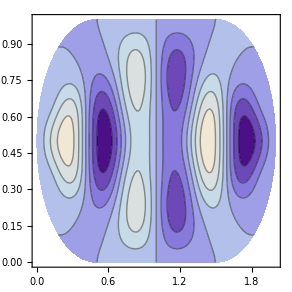

```mathematica
"curvas de nível da autofunção"
ContourPlot[ϕ[x,y],{x,0,A},{y,0,B},RegionFunction->Function[{x,y,z},(b/2)-√(y(b-y))≤x≤a+(b/2)+√(y(b-y))]]
```